```mathematica
Cos[ArcSin[x]]
```

√(1-x^2)

```mathematica
Sin[ArcTan[x]]
```

x/(√(1+x^2))

```mathematica
n*y/(w/Sqrt[1+w^2])+x/.w-> y/(f-x)
```

x+n (f-x) √(1+y^2/(f-x)^2)

```mathematica
FullSimplify[x+n (f-x) √(1+y^2/(f-x)^2)]
```

x+n (f-x) √(1+y^2/(f-x)^2)

```mathematica
Solve[f n == x+n (f-x) √(1+y^2/(f-x)^2),y]
```

{{y→-(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n},{y→(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n}}

```mathematica
Solve[x== (n f)/(n+1)(1-Sqrt[1-((n+1)y^2)/((n-1)f^2)]),y]
```

{{y→-(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n},{y→(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n}}

```mathematica
-(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n/.{f->1.5,n-> 1.3,x-> 0.8}
```

0.540874+0. ⅈ

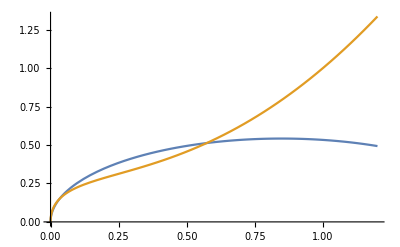

```mathematica
Plot[{-(ⅈ √(-1+n) √x √(-2 f n+x+n x))/n/.{f->1.5,n-> 1.3},Sqrt[x]-x+x^2},{x,0,1.2}]
```

```mathematica
Solve[1.25== 1.5*Sqrt[x],x]
```

{{x→0.694444}}

```mathematica
D[1.5Sqrt[x],x]/.x-> 1.25
```

0.67082

```mathematica
0.6708203932499369*0.6944444444444444
```

0.465847

```mathematica
1.25+0.6708203932499369*x-0.4658474953124562/.x-> 0.3
```

0.985399

```mathematica
FullSimplify[((n f-x)/n)^2-(f-x)^2]
```

-((-1+n) x (-2 f n+x+n x))/n^2

```mathematica
FullSimplify[Solve[y^2 == -((-1+n) x (-2 f n+x+n x))/n^2,x]]
```

{{x→(n (f (-1+n)+n √(((-1+n) (f^2 (-1+n)-(1+n) y^2))/n^2)))/(-1+n^2)},{x→-(n (f-f n+n √(((-1+n) (f^2 (-1+n)-(1+n) y^2))/n^2)))/(-1+n^2)}}